```mathematica
DSolve[{(-x^2+x-3/16)*y'[x]-x*(y[x]-1)==0,y[1]==2},y[x],x]
```

{{y[x]→(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}

```mathematica
(-x^2+x-3/16)*D[1+Exp[3*(x-1)/(16*0.01)]]-x*(1+Exp[3*(x-1)/(16*0.01)])+x
```

x-(1+ⅇ^(18.75 (-1+x))) x+(1+ⅇ^(18.75 (-1+x))) (-3/16+x-x^2)

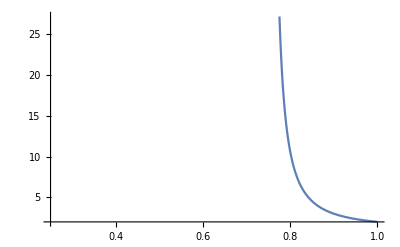

```mathematica
Plot[1+(Sqrt[12x−3]/(3*(4x−3)^(3/2))),{x,1/4,1}]
```

```mathematica
{{y[x]->(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}(*Second boundary condition*)
```

{{y[x]→(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}

```mathematica
{{y[x]->(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}(*First boundary condition*)
```

{{y[x]→(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}

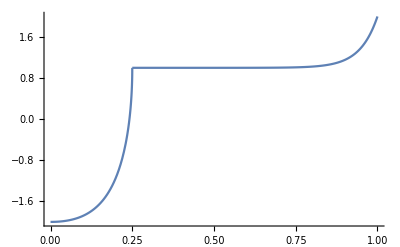

```mathematica
Show[Plot[1+Exp[3*(x-1)/(16*0.01)],{x,1/4,1},PlotRange->All],Plot[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),{x,0,1/4},PlotRange->All]]
```

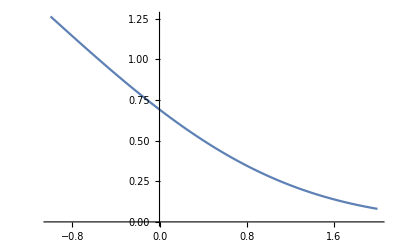

```mathematica
Plot[ⅇ^(-x^2/4)  HermiteH[-3/2,x/2],{x,-1,2}]
```

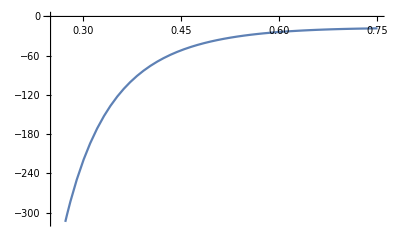

```mathematica
Plot[(-1/(4 x^(3/2))+√x)*(-9 √6 )+ⅇ^(-x^2/4) (-15/(4 x^(7/2))+1/x^(3/2)) ,{x,1/4,3/4}]
```

```mathematica
(-1/(4 x^(3/2))+√x)*(-9 √6 )+ⅇ^(-x^2/4) (-15/(4 x^(7/2))+1/x^(3/2))*c /.x-> 3/4
```

-9 √6 (-2/(3 √3)+(√3)/2)-(136 c)/(9 √3 ⅇ^(9/64))

```mathematica
Solve[-(28 √2 c)/ⅇ^(1/16)==0 &&-9 √6 (-2/(3 √3)+(√3)/2)-(136 c)/(9 √3 ⅇ^(9/64))==0 ,c]
```

Solve::ivar: 1/4 is not a valid variable.

Solve[-(28 √2 c)/ⅇ^(1/16)==0,c,{x,1/4,3/4}]

```mathematica
Solve[-18*Sqrt[3]*Sqrt[-s+1/4]/Sqrt[2]==c*Sqrt[-s+1/4],c]
```

{{c→-9 √6}}

```mathematica
(*Corner layer*)
```

```mathematica
AsymptoticDSolveValue[{z''[x]+(x*z'[x]/2)-((z[x])/4)==0},z[x],{x,-Infinity,5}]
```

(-315/(128 (-x)^(11/2))-15/(32 (-x)^(7/2))-1/(4 (-x)^(3/2))+√-x) C[1]+ⅇ^(-x^2/4) (-45045/(128 (-x)^(15/2))+945/(32 (-x)^(11/2))-15/(4 (-x)^(7/2))+1/(-x)^(3/2)) C[2]

```mathematica
{{z[x]->1+ⅇ^(-x^2/4) C[1] HermiteH[-3/2,x/2]+ⅇ^(-x^2/4) C[2] Hypergeometric1F1[3/4,1/2,x^2/4]}}(*Corner layer*)
```

{{z[x]→1+ⅇ^(-x^2/4) C[1] HermiteH[-3/2,x/2]+ⅇ^(-x^2/4) C[2] Hypergeometric1F1[3/4,1/2,x^2/4]}}

```mathematica
(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)-(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2)
```

(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)-(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2)

```mathematica
(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)+(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2)
```

(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)+(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2)

```mathematica
Solve[(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)+(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2) && (-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)==-1+(√(-16382+x) BesselI[1,√2 √(-16382+x)] C[1])/(√2)-(√(-16382+x) BesselK[1,√2 √(-16382+x)] C[2])/(√2),{C[1],C[2]}]
```

{{C[1]→-(2 √2 (7 √3 √(1-4 x)-3 (3-4 x)^(3/2)))/(3 (3-4 x)^(3/2) √(-16382+x) BesselI[1,√2 √(-16382+x)]),C[2]→(13 √(2/3) √(1-4 x))/((3-4 x)^(3/2) √(-16382+x) BesselK[1,√2 √(-16382+x)])}}

```mathematica
-1+(√(2+x) BesselI[1,√2 √(2+x)] C[1])/(√2)-(√(2+x) BesselK[1,√2 √(2+x)] C[2])/(√2)/.C[1]->-(2 √2 (7 √3 √(1-4 x)-3 (3-4 x)^(3/2)))/(3 (3-4 x)^(3/2) √(-16382+x) BesselI[1,√2 √(-16382+x)])/.C[2]->-(13 √(2/3) √(1-4 x))/((3-4 x)^(3/2) √(-16382+x) BesselK[1,√2 √(-16382+x)])
```

-1-(2 (7 √3 √(1-4 x)-3 (3-4 x)^(3/2)) √(2+x) BesselI[1,√2 √(2+x)])/(3 (3-4 x)^(3/2) √(-16382+x) BesselI[1,√2 √(-16382+x)])+(13 √(1-4 x) √(2+x) BesselK[1,√2 √(2+x)])/(√3 (3-4 x)^(3/2) √(-16382+x) BesselK[1,√2 √(-16382+x)])

```mathematica
N[-1-(2 (7 √3 √(1-4 x)-3 (3-4 x)^(3/2)) √(2+x) BesselI[1,√2 √(2+x)])/(3 (3-4 x)^(3/2) √(-16382+x) BesselI[1,√2 √(-16382+x)])+(13 √(1-4 x) √(2+x) BesselK[1,√2 √(2+x)])/(√3 (3-4 x)^(3/2) √(-16382+x) BesselK[1,√2 √(-16382+x)])]
```

-1.-(0.666667 (12.1244 √(1.-4. x)-3. (3.-4. x)^(3/2)) √(2.+x) BesselI[1.,1.41421 √(2.+x)])/((3.-4. x)^(3/2) √(-16382.+x) BesselI[1.,1.41421 √(-16382.+x)])+(7.50555 √(1.-4. x) √(2.+x) BesselK[1.,1.41421 √(2.+x)])/((3.-4. x)^(3/2) √(-16382.+x) BesselK[1.,1.41421 √(-16382.+x)])

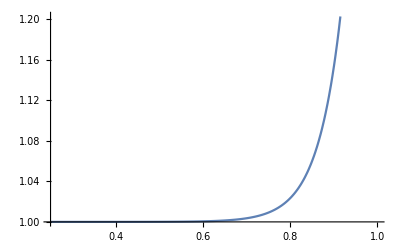

```mathematica
Plot[1+Exp[3*(x-1)/(16*0.01)],{x,1/4,1}]
```